```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

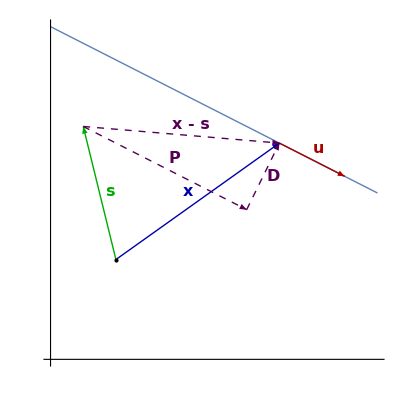

```mathematica
bold = Style[ #, Bold] &;
fs = Style[#, FontSize-> 16]&;

o={0,0};
o2 = {0.2,0.3};
x1 ={0,1};
x2={1,0.5};
d = x2 - x1;
dhat = d/Norm[d];
s = {0.1,0.7};
u0 = x1 + 0.7 d;
u1 = x1 + 0.9 d;

cross2[a_, b_] := Cross[{a[[1]], a[[2]], 0},{b[[1]], b[[2]], 0}];
killz[a_] := {a[[1]], a[[2]]};

(*u1 - s
dhat*)
proj = ((u0 - s). dhat)dhat;
rej = u0 - s - proj;
(*rej = killz[-cross2[cross2[x1 + 0.7 d - s, d / Norm[d]],d / Norm[d]]]*)

p=ParametricPlot[x1 + t d, {t, 0, 1}, GridLines->Automatic, AspectRatio->1, PlotRange -> {{0,1},{0,1}}, Ticks -> None, PlotStyle-> Thick];
plot1 = Show[{
p,
Graphics[{
Thick,
Arrowheads[Large],
Blue// Darker,
Arrow[{o2, u0}],
Text["x"// bold//fs, (o2+ u0)/2 + 0.03 {-1,1}],
Red// Darker,
Arrow[{u0, u1}],
Text["u"// bold//fs, (u0+ u1)/2 + 0.03 {0.6,1.1}],
Green //Darker,
Arrow[{o2,s}],
Text["s"// bold//fs, (o2 + s)/2 + 0.03{1,0.2}],
Dashed,
Purple// Darker,
Arrow[{s,u0}],
Text["x - s"// bold//fs, (s + u0)/2 + 0.03{1,1}],
Arrow[{s,s +proj}],
Text["P"// bold//fs, (s + s +proj)/2 + 0.03{1,1}],
Arrow[{s +proj, u0}],
Text["D"// bold//fs, (s +proj+ u0)/2 + 0.03{1,0}],
Black,
PointSize[Large],
Point[o2]
}]
}]
```

```mathematica
peeters`exportForLatex["distanceToLineFig1", plot1]
```

{distanceToLineFig1.eps,distanceToLineFig1pn.png}